d:\triangle\Votes\13\19\GoodBadInVotedValues-13-19.txt

d:\triangle\Votes\13\19\VotedValues.txt

Null

{97,{a→0.968204,b→1202.4,c→85.6569,d→167.563}}

{1.03284,0.000831672,0.0116745,0.0059679}

0.968204+0.000831672/(0.0116745 x-1.95621)

3 | 0.000301623
5 | -0.000498318
7 | -0.000857372
11 | 0.00177488
13 | 0.000453255
17 | -0.000438978
19 | -0.000340654
23 | -0.000406114
29 | -0.000302552
31 | -0.000203442
37 | 0.0000508676
41 | 0.000082168
43 | 0.000083708
47 | 0.000145489
53 | 0.000160097
59 | 0.000115927
61 | 0.0000791896
67 | 2.59324×10^-6
71 | -0.0000568243
73 | -0.000145539

3 | 0.649356
5 | 0.728959
7 | 0.778659
11 | 0.834274
13 | 0.854164
17 | 0.881268
19 | 0.890738
23 | 0.905518
29 | 0.9205
31 | 0.924214
37 | 0.933017
41 | 0.937578
43 | 0.939552
47 | 0.942929
53 | 0.947069
59 | 0.950379
61 | 0.951351
67 | 0.953868
71 | 0.955301
73 | 0.956013

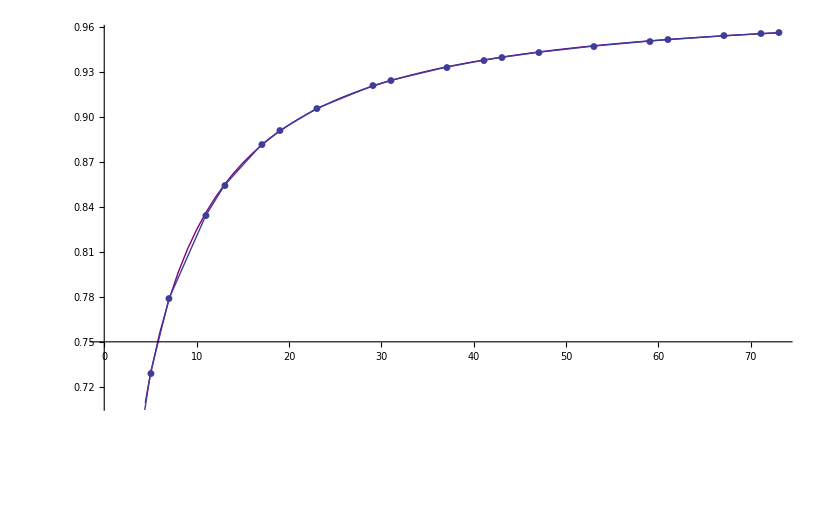

```mathematica
Show[
Table[
Module[
{lastPrime=21,
factors,
methodTemplate = a+(1/b) / Zeta [ (x -d)/c], 
dataTable},
Print[CloseStreams[]];
dataTable=Table[{p, RatioFor[{prime,p},{p}]}, {p, Select[Prime[Range[2,lastPrime]],#≠prime&]}];
factors=FindFit[dataTable,
 methodTemplate,
{a,b,c,d},
x,
PrecisionGoal->Infinity,
MaxIterations->10000
];
Print[{prime, factors}];
Print[N[1/{a,b,c,d}]/.factors];
Print[FullSimplify[methodTemplate/.factors]];
Print[TableForm[
Table[{x, methodTemplate- RatioFor[{prime,x},{x}]/.factors },
{x,Select[Prime[Range[2,lastPrime]],#≠prime&]}]
]
];
Show[
{
ListLinePlot[
Table[methodTemplate/.factors,{x,1,Prime[lastPrime]}],
PlotStyle->Purple
]
,
ListLinePlot[
With[
{t=Table[{p, RatioFor[{prime,p},{p}]}, {p, Select[Prime[Range[2,lastPrime]],#≠prime&]}]},
Print[TableForm [t]];
t
],
PlotMarkers->Automatic
]
}
]
]
,{prime, {97}}
]
]
```

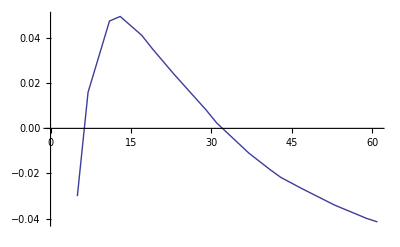

```mathematica
ListLinePlot[{{5, -0.030051440870147772}, {7, 0.015984087323621665}, {11, 0.04759087703962628}, {13, 0.04960766915553272}, {17, 0.04130217134674119}, {19, 0.03529797973374471}, {23, 0.024111247715152828}, {29, 0.00823920884960394}, {31, 0.002406779689461125}, {37, -0.010950417544004942}, {41, -0.01835428187919419}, {43, -0.02177149199275963}, {47, -0.026822234492973607}, {53, -0.03399822970230293}, {59, -0.039927979288463256}, {61, -0.04145170174445312}}]
```

```mathematica
PrimeGoodPlotForTuple[{53,97},{53}]
```

```mathematica
Show[
Table[
Module[
{lastPrime=50,
factors,
methodTemplate = a+(1/b) / Zeta [ (x )/c-d], 
dataTable},
Print[CloseStreams[]];
dataTable=Table[{p, RatioFor[{prime,p},{prime}]}, {p, Select[Prime[Range[2,lastPrime]],#≠prime&]}];
factors=FindFit[dataTable,
 methodTemplate,
{a,b,c,d},
x,
PrecisionGoal->Infinity,
MaxIterations->10000
];
Print[{prime, factors}];
Print[N[1/{a,b,c,d}]/.factors];
Print[TableForm[
Table[{x, methodTemplate- RatioFor[{prime,x},{prime}]/.factors },
{x,Select[Prime[Range[2,lastPrime]],#≠prime&]}]
]
];
ListLinePlot[{
Table[{x,methodTemplate/.factors},{x,1,Prime[lastPrime],0.1}],
Table[{p, RatioFor[{prime,p},{prime}]}, {p, Select[Prime[Range[2,lastPrime]],#≠prime&]}]},
PlotMarkers->Automatic
]
]
,{prime, {97}}
]
]
```

Null

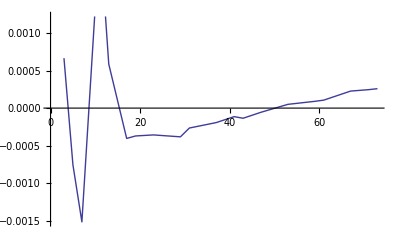

```mathematica
ListLinePlot[{{3, 0.0006661602637337873}, {5, -0.0007572196156637808}, {7, -0.0015179855826433588}, {11, 0.002325646435440915}, {13, 0.0005874093266880626}, {17, -0.0004046623508948341}, {19, -0.0003716051087377936}, {23, -0.0003578443899109225}, {29, -0.0003833795364169383}, {31, -0.0002658856450202911}, {37, -0.00019328365148506277}, {41, -0.00011394631206772948}, {43, -0.00013535211338804726}, {47, -0.00005559715855498956}, {53, 0.000049989549367596836}, {59, 0.00009005137695858659}, {61, 0.00010601594059400296}, {67, 0.00022680680350331897}, {71, 0.00024578776722106524}, {73, 0.0002588940000344646}}]
```